```mathematica
EdgesInColor[edges_,color_]:=Map[#->Directive[color,Thick]&,edges]
```

```mathematica
EdgesInColor2[assoc_,edges_,color_]:=Block[{result=assoc},
Table[
If[KeyExistsQ[result,e],
result[e]=Join[result[e],color]
,
result[e]=color
]
,{e,edges}
];
result
]
```

```mathematica
BlurAssoc[assoc_]:=Block[{result=assoc},
Table[
result[k]={Thickness[0.015],If[Length[result[k]]==1,result[k],{Blend[result[k]]}]}
,{k,Keys[result]}
];
result]
```

```mathematica
AssocToRule[assoc_]:=Table[
k->assoc[k]
,{k,Keys[assoc]}
]
```

```mathematica
AssocToRule2[assoc_]:=Table[
k->Tooltip[k,assoc[k]]
,{k,Keys[assoc]}
]
```

```mathematica
SummarizeAssoc[assoc_]:=Multicolumn[
Sort[
Table[
k->assoc[k]
,{k,Keys[assoc]}
]]
]
```

```mathematica
Length[QuadrilateralsWithPattern[5,5]]
```

1

```mathematica
QuadrilateralsWithPattern[7,5]//Length
```

16

```mathematica
ShowForNodes[nodes_,take_:1]:=Monitor[
Sort[
Flatten[
Table[
Table[
Table[
Table[
Table[
Block[
{
e1=EdgeList[GraphComplement[GraphFromSets[part1]]],
e2=EdgeList[GraphComplement[GraphFromSets[part2]]],
e3=EdgeList[GraphComplement[GraphFromSets[part3]]],
e4=EdgeList[GraphComplement[GraphFromSets[part4]]],
e5=EdgeList[GraphComplement[GraphFromSets[part5]]],
colors=Association[]
},
colors=EdgesInColor2[colors,e1,{Yellow}];
colors=EdgesInColor2[colors,e2,{Red}];
colors=EdgesInColor2[colors,e3,{Green}];
colors=EdgesInColor2[colors,e4,{Blue}];
colors=EdgesInColor2[colors,e5,{Orange}];
Block[
{
gf=Select[FindFullFormula[ EdgeDelete[CompleteGraph[nodes],DeleteDuplicates[Join[e1,e2,e3,e4,e5]]]], SymbolLevel[#]==4&],
first,
efirst,
labels,
colors2,
colors3,
summary,
summary2
},
Table[
colors2=colors;
colors3=colors2;
summary2=Column[Table[e<->colors3[e],{e,{1<->3,1<->4,2<->4,2<->5,3<->5}}]];
colors3=KeyDrop[colors3,{1<->3,1<->4,2<->4,2<->5,3<->5}];
summary=SummarizeAssoc[colors3];
labels=AssocToRule2[colors2];
colors2=BlurAssoc[colors2];
(*first=First[Select[gf,HasTrianglePattern[SymbolToSets[#]]&]];*)
efirst=EdgeList[GraphComplement[GraphFromSets[SymbolToSets[first]]]];
colors2=EdgesInColor2[colors2,efirst,{Thickness[0.08]}];
{Length[gf],
first,
summary2,
summary,
Labeled[
CompleteGraph[nodes,
EdgeStyle->AssocToRule[colors2],
VertexLabels->"Name",
EdgeLabels->labels,
ImageSize->400
],
Column[{Style[SetsToLabel[part1],Darker[Yellow]],Style[SetsToLabel[part2],Red],Style[SetsToLabel[part3],Darker[Green]],Style[SetsToLabel[part4],Blue],Style[SetsToLabel[part5],Orange],
Length[gf],
Map[With[{s=SymbolToSets[#]},
{Style[SetsToLabel2[s],If[HasQuadrilateralPattern[s],Blue,If[HasTrianglePattern[s],Red,Black]]],
With[{pattern=
WhichQuadrilateralPattern[s]},
If[pattern==-1,WhichTrianglePattern[s],Framed[pattern]]
]
}
]&,gf]}]
]
},
{first,Select[gf,HasTrianglePattern[SymbolToSets[#]]&]}
]
]
],
{part5,Take[QuadrilateralsWithPattern[nodes,5],take]}
],
{part4,Take[QuadrilateralsWithPattern[nodes,4],take]}
],
{part3,Take[QuadrilateralsWithPattern[nodes,3],take]}
],
{part2,Take[QuadrilateralsWithPattern[nodes,2],take]}
],
{part1,Take[QuadrilateralsWithPattern[nodes,1],take]}
],3]
],
{part1,part2,part3,part4,part5}
]
```

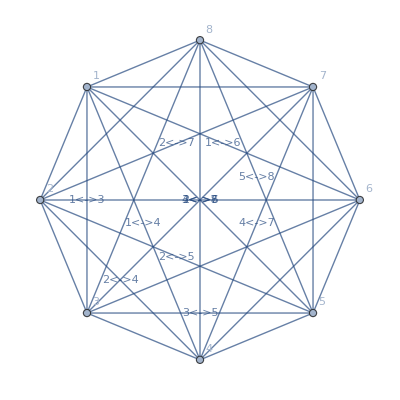
{{{{8,v16x247x35x8,1<->3<->{RGBColor[1, 1, 0]}
1<->4<->{RGBColor[0, 0, 1]}
2<->4<->{RGBColor[1, 0, 0]}
2<->5<->{RGBColor[1, 0.5, 0]}
3<->5<->{RGBColor[0, 1, 0]},1<->6→{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 0.5, 0]} | 3<->7→{RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0.5, 0]} | 5<->8→{RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1]}
2<->6→{RGBColor[1, 1, 0],RGBColor[0, 0, 1]} | 4<->7→{RGBColor[1, 1, 0]} | 
2<->7→{RGBColor[0, 1, 0]} | 4<->8→{RGBColor[0, 1, 0],RGBColor[1, 0.5, 0]} | ,-Graphics-13♁26♁47♁58
16♁24♁37♁58
16♁27♁35♁48
14♁26♁37♁58
16♁25♁37♁48
8
{{16♁27♁35♁48,5},{16♁25♁37♁48,4},{16♁247♁58,3},{16♁24♁37♁58,3},{16♁247♁35,5},{14♁26♁37♁58,2},{13♁26♁47♁58,1},{13♁247♁58,1}}},{8,v13x247x58x6,1<->3<->{RGBColor[1, 1, 0]}
1<->4<->{RGBColor[0, 0, 1]}
2<->4<->{RGBColor[1, 0, 0]}
2<->5<->{RGBColor[1, 0.5, 0]}
3<->5<->{RGBColor[0, 1, 0]},1<->6→{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 0.5, 0]} | 3<->7→{RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0.5, 0]} | 5<->8→{RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1]}
2<->6→{RGBColor[1, 1, 0],RGBColor[0, 0, 1]} | 4<->7→{RGBColor[1, 1, 0]} | 
2<->7→{RGBColor[0, 1, 0]} | 4<->8→{RGBColor[0, 1, 0],RGBColor[1, 0.5, 0]} | ,-Graphics-13♁26♁47♁58
16♁24♁37♁58
16♁27♁35♁48
14♁26♁37♁58
16♁25♁37♁48
8
{{16♁27♁35♁48,5},{16♁25♁37♁48,4},{16♁247♁58,3},{16♁24♁37♁58,3},{16♁247♁35,5},{14♁26♁37♁58,2},{13♁26♁47♁58,1},{13♁247♁58,1}}}}}}

```mathematica
ShowForNodes[8,1]
```